```mathematica
(* Expansion in Bessel functions *)
(* ----------------------------------- *)
Off[FindRoot::lstol]
```

```mathematica
(* this is the function we will expand *)
(* ------------------------------------------ *)
v[x_]:=1+x+x^2
```

```mathematica
(* zero(m,n)=n'th zero of j_m(x) *)
(* ---------------------------------- *)
zero[m_,n_]:=zero[m,n]=x/.FindRoot[BesselJ[m,x]==0,{x,n*Pi}]
```

```mathematica
Table[zero[0,i],{i,1,5}]
```

{2.40483,5.52008,8.65373,11.7915,14.9309}

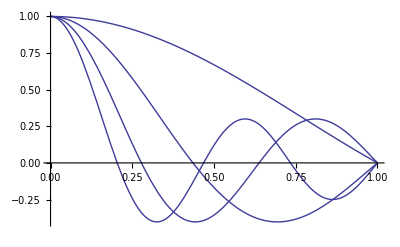

```mathematica
(* complete set of functions, J_0(x_0^n*x *)
(* --------------------------------------------- *)
Plot[Table[BesselJ[0,x*zero[0,n]],{n,1,4}],{x,0,1}]
```

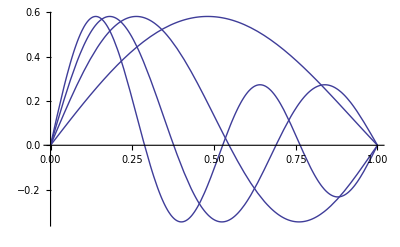

```mathematica
(* same for J_1 *)
(* --------------- *)
Plot[Table[BesselJ[1,x*zero[1,n]],{n,1,4}],{x,0,1}]
```

```mathematica
(* normalisation factors *)
(* ------------------------- *)
norm[m_,n_]:=Block[{x0=zero[m,n]},2/BesselJ[m+1,x0]^2]
```

```mathematica
(* expansion coefficient for v(rho) defined above *)
(* ------------------------------------------------------ *)
c[m_,n_]:=c[m,n]=norm[m,n]*Block[{x0=zero[m,n]},NIntegrate[rho*v[rho]*BesselJ[m,x0*rho],{rho,0,1}]]
```

```mathematica
(* Bessel expansion using J_m, first nmax *)
(* --------------------------------------------- *)
vpart[m_,nmax_,x_]:=Sum[c[m,n]*BesselJ[m,zero[m,n]*x],{n,1,nmax}]
```

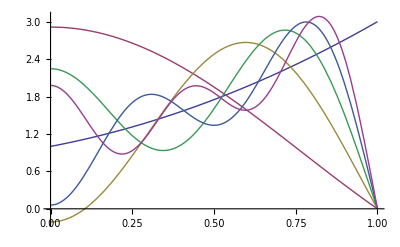

```mathematica
(* first five approximations, using J_0 *)
(* ------------------------------------------- *)
Plot[{v[x],vpart[0,1,x],vpart[0,2,x],vpart[0,3,x],vpart[0,4,x],vpart[0,5,x]},{x,0,1}]
```

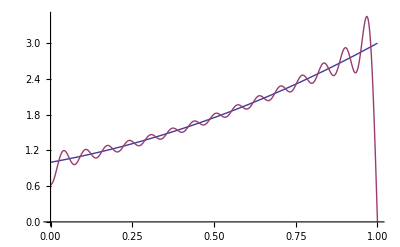

```mathematica
(* a high order approximation, using 30 Bessel fcts *)
(* ---------------------------------------------------------- *)
Plot[{v[x],vpart[0,30,x]},{x,0,1}]
```

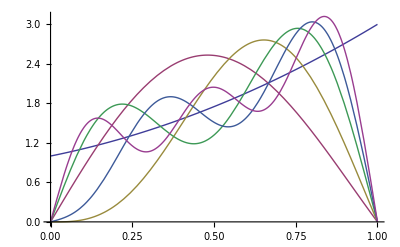

```mathematica
(* same for J_1(x) *)
(* ------------------ *)
Plot[{v[x],vpart[1,1,x],vpart[1,2,x],vpart[1,3,x],vpart[1,4,x],vpart[1,5,x]},{x,0,1}]
```

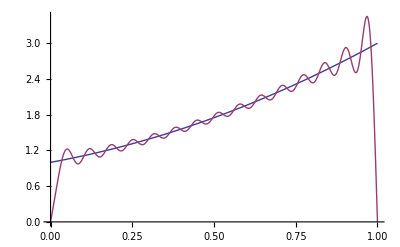

```mathematica
Plot[{v[x],vpart[1,30,x]},{x,0,1}]
```